```mathematica
(*Mathematica*)
```

```mathematica
Clear[t,a,p,aa,bb,z]
```

```mathematica
(* cf: A073058*)
```

```mathematica
(* F. M. Dekking, "Recurrent Sets" ,Advances in Mathematics,vol. 44, no.1,April 1982, page 85, section 4.15*)
```

```mathematica
CompanionMatrix[p_, x_] := Module[{cl=CoefficientList[p, x], deg, m}, cl=Drop[cl/Last[cl], -1]; deg=Length[cl]; If[deg==1, {-cl}, m=RotateLeft[IdentityMatrix[deg]]; m[[ -1]]=-cl; Transpose[m]]];
```

```mathematica
name={"Circulant",{10,{1,2,3}}}
```

{Circulant,{10,{1,2,3}}}

```mathematica
Show[GraphData[name,"Graph","MinimalCrossing"],ImageSize->Full,Background->Black]
```

Show::shx: No graphical objects to show.

Show[{},ImageSize→Full,Background→GrayLevel[0]]

```mathematica
GraphPlot3D[GraphData[name],ImageSize->Full,Background->Black]
```

```mathematica
m=AdjacencyMatrix[GraphData[name]]
```

SparseArray[…]

```mathematica
n0=10
```

10

```mathematica
p0[z_]=CharacteristicPolynomial[AdjacencyMatrix[GraphData[name]],z]
```

-12-100 z-295 z^2-320 z^3+50 z^4+296 z^5+95 z^6-60 z^7-30 z^8+z^10

```mathematica
m0=Transpose[CompanionMatrix[p0[z],z] ]
```

{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{12,100,295,320,-50,-296,-95,60,30,0}}

```mathematica
AdjacencyGraph[m]
```

```mathematica
Eigenvalues[m]
```

{6,1/2 (-3-√5),1/2 (-3-√5),-2,1/2 (1+√5),1/2 (1+√5),1/2 (1-√5),1/2 (1-√5),1/2 (-3+√5),1/2 (-3+√5)}

```mathematica
(* make polynomial*)
```

```mathematica
Factor[Det[m-x*IdentityMatrix[n0]]]
```

(-6+x) (2+x) (-1-x+x^2)^2 (1+3 x+x^2)^2

```mathematica
(* solve Polynomial*)
```

```mathematica
z=x/.NSolve[CharacteristicPolynomial[m,x]==0,x][[1]]
```

-2.61803

```mathematica
v=Table[N[{Cos[2*Pi*i/10],Sin[2*Pi*i/10]}],{i,10}]
```

{{0.809017,0.587785},{0.309017,0.951057},{-0.309017,0.951057},{-0.809017,0.587785},{-1.,0.},{-0.809017,-0.587785},{-0.309017,-0.951057},{0.309017,-0.951057},{0.809017,-0.587785},{1.,0.}}

```mathematica
NSolve[CharacteristicPolynomial[m,x]==0,x]
```

{{x→-2.61803},{x→-2.61803},{x→-2.},{x→-0.618034},{x→-0.618034},{x→-0.381966},{x→-0.381966},{x→1.61803},{x→1.61803},{x→6.}}

```mathematica
Clear[s]
ss=Table[Union[Table[If[m[[i,j]]==1||j==i,j,Nothing],{j,10}]],{i,10}]
```

{{1,2,3,4,8,9,10},{1,2,3,4,5,9,10},{1,2,3,4,5,6,10},{1,2,3,4,5,6,7},{2,3,4,5,6,7,8},{3,4,5,6,7,8,9},{4,5,6,7,8,9,10},{1,5,6,7,8,9,10},{1,2,6,7,8,9,10},{1,2,3,7,8,9,10}}

```mathematica
Table[s[i]=ss[[i]],{i,10}]
```

{{1,2,3,4,8,9,10},{1,2,3,4,5,9,10},{1,2,3,4,5,6,10},{1,2,3,4,5,6,7},{2,3,4,5,6,7,8},{3,4,5,6,7,8,9},{4,5,6,7,8,9,10},{1,5,6,7,8,9,10},{1,2,6,7,8,9,10},{1,2,3,7,8,9,10}}

```mathematica
w=Flatten[Table[s[i],{i,10}]]
```

{1,2,3,4,8,9,10,1,2,3,4,5,9,10,1,2,3,4,5,6,10,1,2,3,4,5,6,7,2,3,4,5,6,7,8,3,4,5,6,7,8,9,4,5,6,7,8,9,10,1,5,6,7,8,9,10,1,2,6,7,8,9,10,1,2,3,7,8,9,10}

```mathematica
t[a_] :=Flatten[s/@a];         
p[0]={1};p[1]=t[p[0]];
p[n_]:=t[p[n-1]]
aa=p[7];
```

```mathematica
Length[aa]
```

823543

```mathematica
bb=aa/. 1->v[[1]]/. 2->v[[2]]/. 3->v[[3]]/. 4->v[[4]]/. 5->v[[5]]/. 6->v[[6]]/. 7->v[[7]]/. 8->v[[8]]/. 9->v[[9]]/. 10->v[[10]];
```

```mathematica
cc=FoldList[Plus,{0,0},bb];
```

```mathematica
g0=ListPlot[cc,ColorFunction->Hue,Axes->True,PlotStyle->PointSize[0.001],ImageSize->{2000,2000},PlotRange->All];
```

```mathematica
(* color seperation*)
```

```mathematica
allColors=ColorData["Legacy"][[3,1]];
firstCols={"Red","ManganeseBlue","Blue","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow"};
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
cc=FoldList[Plus,{0,0},bb];
dd=Flatten[ParallelTable[{cols[[aa[[n]]]],PointSize[0.001],Point[cc[[n]]]},{n,Min[Length[cc],Length[aa]]}]];
```

```mathematica
g2=Show[Graphics[dd],ImageSize->{2000,2000},Background->Black];
```

```mathematica
Export["10symbol_Circulant10_123_substitution_level7_grid.jpg",GraphicsGrid[{{g0},{g2}},ImageSize->{{2000,4000}}]]
```

```mathematica
(*end*)
```

```mathematica
(*Mathematica*)
```

```mathematica
Clear[t,a,p,aa,bb,z]
```

```mathematica
(* cf: A073058*)
```

```mathematica
(* F. M. Dekking, "Recurrent Sets" ,Advances in Mathematics,vol. 44, no.1,April 1982, page 85, section 4.15*)
```

```mathematica
CompanionMatrix[p_, x_] := Module[{cl=CoefficientList[p, x], deg, m}, cl=Drop[cl/Last[cl], -1]; deg=Length[cl]; If[deg==1, {-cl}, m=RotateLeft[IdentityMatrix[deg]]; m[[ -1]]=-cl; Transpose[m]]];
```

```mathematica
name={"Circulant",{10,{1,2,3}}}
```

{Circulant,{10,{1,2,3}}}

```mathematica
Show[GraphData[name,"Graph","MinimalCrossing"],ImageSize->Full,Background->Black]
```

Show::shx: No graphical objects to show.

Show[{},ImageSize→Full,Background→GrayLevel[0]]

```mathematica
GraphPlot3D[GraphData[name],ImageSize->Full,Background->Black]
```

```mathematica
m=AdjacencyMatrix[GraphData[name]]
```

SparseArray[…]

```mathematica
n0=10
```

10

```mathematica
p0[z_]=CharacteristicPolynomial[AdjacencyMatrix[GraphData[name]],z]
```

-12-100 z-295 z^2-320 z^3+50 z^4+296 z^5+95 z^6-60 z^7-30 z^8+z^10

```mathematica
m0=Transpose[CompanionMatrix[p0[z],z] ]
```

{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{12,100,295,320,-50,-296,-95,60,30,0}}

```mathematica
AdjacencyGraph[m]
```

```mathematica
Eigenvalues[m]
```

{6,1/2 (-3-√5),1/2 (-3-√5),-2,1/2 (1+√5),1/2 (1+√5),1/2 (1-√5),1/2 (1-√5),1/2 (-3+√5),1/2 (-3+√5)}

```mathematica
m1=Transpose[m]
```

SparseArray[…]

```mathematica
(*Transpose is the same: symmetric matrix*)
```

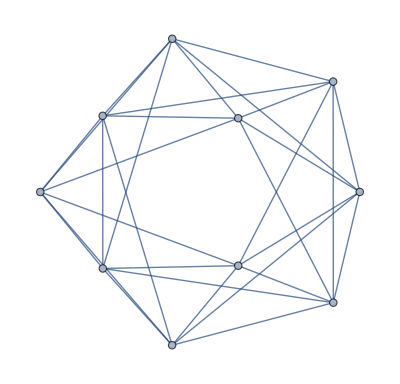

```mathematica
AdjacencyGraph[m1]
```

```mathematica
Eigenvalues[m1]
```

{6,1/2 (-3-√5),1/2 (-3-√5),-2,1/2 (1+√5),1/2 (1+√5),1/2 (1-√5),1/2 (1-√5),1/2 (-3+√5),1/2 (-3+√5)}

```mathematica
(* make polynomial*)
```

```mathematica
Factor[Det[m1-x*IdentityMatrix[n0]]]
```

(-6+x) (2+x) (-1-x+x^2)^2 (1+3 x+x^2)^2

```mathematica
(* solve Polynomial*)
```

```mathematica
z=x/.NSolve[CharacteristicPolynomial[m1,x]==0,x][[1]]
```

-2.61803

```mathematica
v=Table[N[{Cos[2*Pi*i/10],Sin[2*Pi*i/10]}],{i,10}]
```

{{0.809017,0.587785},{0.309017,0.951057},{-0.309017,0.951057},{-0.809017,0.587785},{-1.,0.},{-0.809017,-0.587785},{-0.309017,-0.951057},{0.309017,-0.951057},{0.809017,-0.587785},{1.,0.}}

```mathematica
NSolve[CharacteristicPolynomial[m1,x]==0,x]
```

{{x→-2.61803},{x→-2.61803},{x→-2.},{x→-0.618034},{x→-0.618034},{x→-0.381966},{x→-0.381966},{x→1.61803},{x→1.61803},{x→6.}}

```mathematica
Clear[s]
ss=Table[Union[Table[If[m1[[i,j]]==1||j==i,j,Nothing],{j,10}]],{i,10}]
```

{{1,2,3,4,8,9,10},{1,2,3,4,5,9,10},{1,2,3,4,5,6,10},{1,2,3,4,5,6,7},{2,3,4,5,6,7,8},{3,4,5,6,7,8,9},{4,5,6,7,8,9,10},{1,5,6,7,8,9,10},{1,2,6,7,8,9,10},{1,2,3,7,8,9,10}}

```mathematica
Table[s[i]=Reverse[ss[[i]]],{i,10}]
```

{{10,9,8,4,3,2,1},{10,9,5,4,3,2,1},{10,6,5,4,3,2,1},{7,6,5,4,3,2,1},{8,7,6,5,4,3,2},{9,8,7,6,5,4,3},{10,9,8,7,6,5,4},{10,9,8,7,6,5,1},{10,9,8,7,6,2,1},{10,9,8,7,3,2,1}}

```mathematica
w=Reverse[Flatten[Table[s[i],{i,10}]]]
```

{1,2,3,7,8,9,10,1,2,6,7,8,9,10,1,5,6,7,8,9,10,4,5,6,7,8,9,10,3,4,5,6,7,8,9,2,3,4,5,6,7,8,1,2,3,4,5,6,7,1,2,3,4,5,6,10,1,2,3,4,5,9,10,1,2,3,4,8,9,10}

```mathematica
t[a_] :=Flatten[s/@a];         
p[0]={1};p[1]=t[p[0]];
p[n_]:=t[p[n-1]]
aa=p[7];
```

```mathematica
Length[aa]
```

823543

```mathematica
bb=aa/. 1->v[[1]]/. 2->v[[2]]/. 3->v[[3]]/. 4->v[[4]]/. 5->v[[5]]/. 6->v[[6]]/. 7->v[[7]]/. 8->v[[8]]/. 9->v[[9]]/. 10->v[[10]];
```

```mathematica
cc=FoldList[Plus,{0,0},bb];
```

```mathematica
g0=ListPlot[cc,ColorFunction->Hue,Axes->True,PlotStyle->PointSize[0.001],ImageSize->{2000,2000},PlotRange->All];
```

```mathematica
(* color seperation*)
```

```mathematica
allColors=ColorData["Legacy"][[3,1]];
firstCols={"Red","ManganeseBlue","Blue","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow"};
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
cc=FoldList[Plus,{0,0},bb];
dd=Flatten[ParallelTable[{cols[[aa[[n]]]],PointSize[0.001],Point[cc[[n]]]},{n,Min[Length[cc],Length[aa]]}]];
```

```mathematica
g2=Show[Graphics[dd],ImageSize->{2000,2000},Background->Black];
```

```mathematica
Export["10symbol_Circulant10_123_reverse_substitution_level7_grid.jpg",GraphicsGrid[{{g0},{g2}},ImageSize->{{2000,4000}}]]
```

10symbol_Circulant10_123_reverse_substitution_level7_grid.jpg

```mathematica
(*end*)
```